# Convolution of Na and K densities

```mathematica
Clear["Global`*"]
```

## Na density from bimodal distribution

Constants

```mathematica
mp=1.6726219*10^-27; (*Proton mass*)
mn=1.674929 * 10^-27; (*Neutron mass*)
mK=19*mp+21*mn;
mNa=11*mp+12*mn;
mReduced=mK*mNa/(mNa+mK);
kB=1.38064852*10^-23;
hbar=1.0545718*10^-34;
ωz=2π 110; (*Hz*)
ωy=2π  78;
ωx=2π  13;
ω=(ωx*ωy*ωz)^(1/3.);
```

Na, K-specific constants that depend on the dataset

```mathematica
xw=65;  (*K x-Gaussian waist, defined as exp(-x^2/2sigma^2) *)
yw=10.8;
zw=10.8; (*From 6/14 short dataset, using integrated masked Gaussian fits*)
```

```mathematica
boxWidth={9,4,3,2,2,2,2,2,2}; (*area of one quadrant*)
boxHeight={3};
pixToMicron=2.5;
```

```mathematica
(*NormBose=4.4605*^-13 ;(*for input in meters*)
NormBose=NormBose*10^18 (*for input micron*)*)
xTF=66; (*micron*)
zTF=8.1;
yTF= zTF*ωz/ωy;

β=1/(kB*131*10^-9); (*Temperature*)
μ=2π*860*hbar; (*Chem pot*)
NBEC=5.6*^5;
(*NTherm=6.7*^5;*)
```

All inputs in microns, output in units of um^-3

```mathematica
fBEC[x_,y_,z_]:=15/(8π xTF yTF zTF)(1-x^2/xTF^2-y^2/yTF^2-z^2/zTF^2)*HeavisideTheta[(1-x^2/xTF^2-y^2/yTF^2-z^2/zTF^2)]
```

```mathematica
fThermU[x_,y_,z_]:=PolyLog[3/2,Exp[-β*Abs[1/2mNa(x^2*ωx^2+y^2*ωy^2+z^2*ωz^2)*10^-12-μ]]]
```

```mathematica
(*Check Norm of BEC*)
NIntegrate[fBEC[x,y,z],{x,-xTF,xTF},{y,-yTF,yTF},{z,-zTF,zTF}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 0.00109863 for the integral and error estimates.

0.999999

## Getting the Boson Thermal normalization:

```mathematica
(*Find normalization of thermals.  Varied the IntLimit around 10; didn't change integral.  tried GlobalAdaptive, LocalAdaptive, and AdaptiveMonteCarlo--> All similar to within 2%*)
IntLimNaTherm=10;
NormBose=8*NIntegrate[fThermU[x,y,z],{x,0,xTF*IntLimNaTherm},{y,0,yTF*IntLimNaTherm},{z,0,zTF*IntLimNaTherm}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

319409.

```mathematica
fTherm[x_,y_,z_]:=1/NormBose PolyLog[3/2,Exp[-β*Abs[μ-1/2mNa(x^2*ωx^2+y^2*ωy^2+z^2*ωz^2)*10^-12]]]
```

## Plots

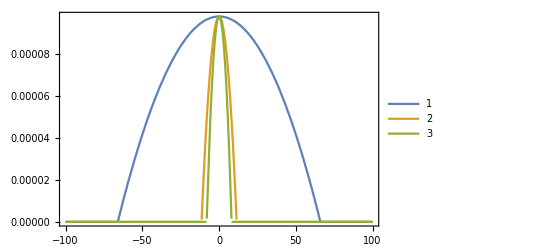

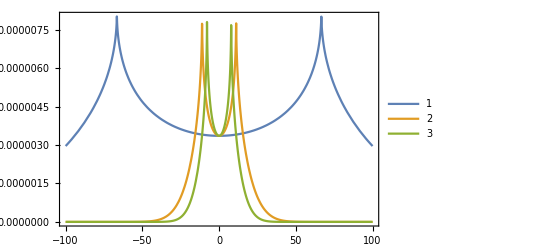

```mathematica
Plot[{fBEC[x,0,0],fBEC[0,x,0],fBEC[0,0,x]},{x,-100,100}, PlotLegends->Automatic]
Plot[{fTherm[x,0,0],fTherm[0,x,0],fTherm[0,0,x]},{x,-100,100}, PlotLegends->Automatic]
```

## Na number density

```mathematica
lambdaDB=(2*π*hbar)/Sqrt[2π mNa/β ] 10^6 (*In micron*)
```

1.00177

In units of um^-3; multiply by 10^12 to get 3D densities in units of cm^-3

```mathematica
nNaBEC[x_,y_,z_]:=NBEC*fBEC[x,y,z]
nNaTherm[x_,y_,z_]:=NormBose/lambdaDB^3*fTherm[x,y,z]
```

```mathematica
NormBose/lambdaDB^3
```

317714.

```mathematica
nNa[x_,y_,z_]:=NBEC*fBEC[x,y,z]+NormBose/lambdaDB^3*fTherm[x,y,z]
```

## K distribution is Maxwell-Boltzmann

```mathematica
(*in micron*)
(*fK[x_,y_,z_]:=((mK β ω^2 10^-12)/(2π))^1.5 Exp[-mK β((x^2ωx^2+y^2ωy^2+z^2ωz^2)*10^-12)/2]*)
```

```mathematica
fK[x_,y_,z_]:=1/(Sqrt[2*π]^3*xw*yw*zw)Exp[-x^2/(2xw^2)-y^2/(2yw^2)-z^2/(2zw^2)]
Integrate[Integrate[Integrate[fK[x,y,z],{z,-Infinity,Infinity}],{y,-Infinity,Infinity}],{x,-Infinity,Infinity}]
```

1.

```mathematica
fK[0,0,0]
```

8.3747×10^-6

## Convolve the two densities

```mathematica
xLimits=Table[0,{i,1,Length[boxWidth]+1}];
xLimits[[2]]=boxWidth[[1]];
For [i=3,i≤Length[boxWidth]+1,i++,xLimits[[i]]=boxWidth[[i-1]]+xLimits[[i-1]]];
xLimitsMicron=xLimits*pixToMicron
```

{0.,22.5,32.5,40.,45.,50.,55.,60.,65.,70.}

Both densities together

```mathematica
densityNaConvolved=Table[0,{i,1,Length[boxWidth]}];
En=Table[0,{i,1,Length[boxWidth]}];
num=Table[0,{i,1,Length[boxWidth]}];
denom=Table[0,{i,1,Length[boxWidth]}];
For[i=1,i≤2, i++,
denom[[i]]=NIntegrate[fK[x,y,z],{x,xLimitsMicron[[i]],xLimitsMicron[[i+1]]},{y,0,2.5*boxHeight[[1]]},{z,0,10*zw}];
Print[denom[[i]]];
num[[i]]    =NIntegrate[fK[x,y,z]*nNa[x,y,z]^(2/3),{x,xLimitsMicron[[i]],xLimitsMicron[[i+1]]},{y,0,2.5*boxHeight[[1]]},{z,0,10*zw},MinRecursion->50,MaxRecursion->100];
Print[num[[i]]];
En[[i]]=(hbar^2(6π^2)^(2/3))/(2mReduced)num[[i]]/denom[[i]]*10^12; (*in m^-2*)
densityNaConvolved[[i]]=(En[[i]]/((hbar^2(6π^2)^(2/3))/(2mReduced)))^1.5*10^-6;(*in cm-^3*)
Print[densityNaConvolved[[i]]]

]
```

0.0173497

0.09456

1.2724×10^13

0.00718609

0.0331195

9.89432×10^12

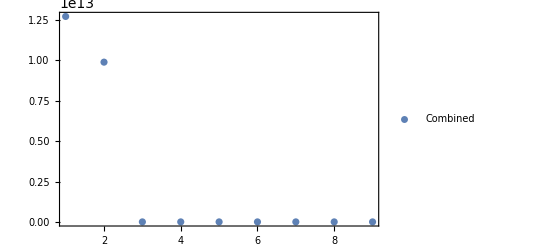

```mathematica
ListPlot[{densityNaConvolved}, PlotRange->All, PlotLegends->{"Combined"}]
```